## Initializing

```mathematica
resfinal={{12.900390625,13.8671875},{19.66796875,20.634765625},{28.369140625,29.3359375},{39.00390625,39.970703125},{50.60546875,51.572265625},{64.140625,65.107421875},{78.642578125,79.609375},{96.044921875,97.01171875},{113.447265625,114.4140625},{133.75,134.716796875},{155.01953125,155.986328125},{178.22265625,179.189453125},{202.392578125,203.359375},{228.49609375,229.462890625},{255.56640625,256.533203125},{285.537109375,286.50390625},{315.5078125,316.474609375},{348.37890625,349.345703125},{382.216796875,383.18359375},{417.98828125,418.955078125},{454.7265625,455.693359375},{493.3984375,494.365234375},{533.037109375,534.00390625},{574.609375,575.576171875},{618.115234375,619.08203125},{663.5546875,664.521484375},{709.9609375,710.927734375},{757.333984375,758.30078125},{807.607421875,808.57421875},{858.84765625,859.814453125},{911.0546875,912.021484375},{965.1953125,966.162109375}};
```

Above is from emcmanis_findcriticalvalues.nb. Run with rho_inf = 20*λ.

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=consts[[2]];
nn=consts[[3]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,ret},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]),
Return[Bisect[F,consts,x0,mid,ϵ]];,
Return[Bisect[F,consts,mid,xf,ϵ]];
];,
Return[mid];
]
]
```

```mathematica
rhoinfs={40*1000.,80*1000.,160*1000.};
```

### Junk?

```mathematica
ParallelTable[{i,j,Evaluate[$KernelID],Timing[Bisect[Critical,{0.01,rhoinfs[[j]],rhoinfs[[j]]/0.01},resfinal[[i,1]],resfinal[[i,2]],10.^(-6)]]},{i,1,2},{j,1,3}]
```

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 20.1514

```mathematica
Parallelize[Table[i,{i,1,10}]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
lcs=Parallelize[Table[Table[{j,Bisect[Critical,{0.01,rhoinfs[[j]],rhoinfs[[j]]/0.01},resfinal[[i,1]],resfinal[[i,2]],10^(-6)]},{j,1,3}],{i,1,Length[resfinal]}]];
```

```mathematica
ParallelTable[i+2,{i,1,10}]
```

{3,4,5,6,7,8,9,10,11,12}

### More good stuff

{tag, rhoinf, lambda1, lambda2} = > {tag, lc[rhoinf]} <- format of this function below me

```mathematica
inputs=Table[Table[{j,rhoinfs[[j]],resfinal[[i,1]],resfinal[[i,2]]},{j,1,3}],{i,1,Length[resfinal]}]
```

{{{1,40000.,12.9004,13.8672},{2,80000.,12.9004,13.8672},{3,160000.,12.9004,13.8672}},{{1,40000.,19.668,20.6348},{2,80000.,19.668,20.6348},{3,160000.,19.668,20.6348}},{{1,40000.,28.3691,29.3359},{2,80000.,28.3691,29.3359},{3,160000.,28.3691,29.3359}},{{1,40000.,39.0039,39.9707},{2,80000.,39.0039,39.9707},{3,160000.,39.0039,39.9707}},{{1,40000.,50.6055,51.5723},{2,80000.,50.6055,51.5723},{3,160000.,50.6055,51.5723}},{{1,40000.,64.1406,65.1074},{2,80000.,64.1406,65.1074},{3,160000.,64.1406,65.1074}},{{1,40000.,78.6426,79.6094},{2,80000.,78.6426,79.6094},{3,160000.,78.6426,79.6094}},{{1,40000.,96.0449,97.0117},{2,80000.,96.0449,97.0117},{3,160000.,96.0449,97.0117}},{{1,40000.,113.447,114.414},{2,80000.,113.447,114.414},{3,160000.,113.447,114.414}},{{1,40000.,133.75,134.717},{2,80000.,133.75,134.717},{3,160000.,133.75,134.717}},{{1,40000.,155.02,155.986},{2,80000.,155.02,155.986},{3,160000.,155.02,155.986}},{{1,40000.,178.223,179.189},{2,80000.,178.223,179.189},{3,160000.,178.223,179.189}},{{1,40000.,202.393,203.359},{2,80000.,202.393,203.359},{3,160000.,202.393,203.359}},{{1,40000.,228.496,229.463},{2,80000.,228.496,229.463},{3,160000.,228.496,229.463}},{{1,40000.,255.566,256.533},{2,80000.,255.566,256.533},{3,160000.,255.566,256.533}},{{1,40000.,285.537,286.504},{2,80000.,285.537,286.504},{3,160000.,285.537,286.504}},{{1,40000.,315.508,316.475},{2,80000.,315.508,316.475},{3,160000.,315.508,316.475}},{{1,40000.,348.379,349.346},{2,80000.,348.379,349.346},{3,160000.,348.379,349.346}},{{1,40000.,382.217,383.184},{2,80000.,382.217,383.184},{3,160000.,382.217,383.184}},{{1,40000.,417.988,418.955},{2,80000.,417.988,418.955},{3,160000.,417.988,418.955}},{{1,40000.,454.727,455.693},{2,80000.,454.727,455.693},{3,160000.,454.727,455.693}},{{1,40000.,493.398,494.365},{2,80000.,493.398,494.365},{3,160000.,493.398,494.365}},{{1,40000.,533.037,534.004},{2,80000.,533.037,534.004},{3,160000.,533.037,534.004}},{{1,40000.,574.609,575.576},{2,80000.,574.609,575.576},{3,160000.,574.609,575.576}},{{1,40000.,618.115,619.082},{2,80000.,618.115,619.082},{3,160000.,618.115,619.082}},{{1,40000.,663.555,664.521},{2,80000.,663.555,664.521},{3,160000.,663.555,664.521}},{{1,40000.,709.961,710.928},{2,80000.,709.961,710.928},{3,160000.,709.961,710.928}},{{1,40000.,757.334,758.301},{2,80000.,757.334,758.301},{3,160000.,757.334,758.301}},{{1,40000.,807.607,808.574},{2,80000.,807.607,808.574},{3,160000.,807.607,808.574}},{{1,40000.,858.848,859.814},{2,80000.,858.848,859.814},{3,160000.,858.848,859.814}},{{1,40000.,911.055,912.021},{2,80000.,911.055,912.021},{3,160000.,911.055,912.021}},{{1,40000.,965.195,966.162},{2,80000.,965.195,966.162},{3,160000.,965.195,966.162}}}

```mathematica
inputs=Flatten[inputs,1]
```

{{1,40000.,12.9004,13.8672},{2,80000.,12.9004,13.8672},{3,160000.,12.9004,13.8672},{1,40000.,19.668,20.6348},{2,80000.,19.668,20.6348},{3,160000.,19.668,20.6348},{1,40000.,28.3691,29.3359},{2,80000.,28.3691,29.3359},{3,160000.,28.3691,29.3359},{1,40000.,39.0039,39.9707},{2,80000.,39.0039,39.9707},{3,160000.,39.0039,39.9707},{1,40000.,50.6055,51.5723},{2,80000.,50.6055,51.5723},{3,160000.,50.6055,51.5723},{1,40000.,64.1406,65.1074},{2,80000.,64.1406,65.1074},{3,160000.,64.1406,65.1074},{1,40000.,78.6426,79.6094},{2,80000.,78.6426,79.6094},{3,160000.,78.6426,79.6094},{1,40000.,96.0449,97.0117},{2,80000.,96.0449,97.0117},{3,160000.,96.0449,97.0117},{1,40000.,113.447,114.414},{2,80000.,113.447,114.414},{3,160000.,113.447,114.414},{1,40000.,133.75,134.717},{2,80000.,133.75,134.717},{3,160000.,133.75,134.717},{1,40000.,155.02,155.986},{2,80000.,155.02,155.986},{3,160000.,155.02,155.986},{1,40000.,178.223,179.189},{2,80000.,178.223,179.189},{3,160000.,178.223,179.189},{1,40000.,202.393,203.359},{2,80000.,202.393,203.359},{3,160000.,202.393,203.359},{1,40000.,228.496,229.463},{2,80000.,228.496,229.463},{3,160000.,228.496,229.463},{1,40000.,255.566,256.533},{2,80000.,255.566,256.533},{3,160000.,255.566,256.533},{1,40000.,285.537,286.504},{2,80000.,285.537,286.504},{3,160000.,285.537,286.504},{1,40000.,315.508,316.475},{2,80000.,315.508,316.475},{3,160000.,315.508,316.475},{1,40000.,348.379,349.346},{2,80000.,348.379,349.346},{3,160000.,348.379,349.346},{1,40000.,382.217,383.184},{2,80000.,382.217,383.184},{3,160000.,382.217,383.184},{1,40000.,417.988,418.955},{2,80000.,417.988,418.955},{3,160000.,417.988,418.955},{1,40000.,454.727,455.693},{2,80000.,454.727,455.693},{3,160000.,454.727,455.693},{1,40000.,493.398,494.365},{2,80000.,493.398,494.365},{3,160000.,493.398,494.365},{1,40000.,533.037,534.004},{2,80000.,533.037,534.004},{3,160000.,533.037,534.004},{1,40000.,574.609,575.576},{2,80000.,574.609,575.576},{3,160000.,574.609,575.576},{1,40000.,618.115,619.082},{2,80000.,618.115,619.082},{3,160000.,618.115,619.082},{1,40000.,663.555,664.521},{2,80000.,663.555,664.521},{3,160000.,663.555,664.521},{1,40000.,709.961,710.928},{2,80000.,709.961,710.928},{3,160000.,709.961,710.928},{1,40000.,757.334,758.301},{2,80000.,757.334,758.301},{3,160000.,757.334,758.301},{1,40000.,807.607,808.574},{2,80000.,807.607,808.574},{3,160000.,807.607,808.574},{1,40000.,858.848,859.814},{2,80000.,858.848,859.814},{3,160000.,858.848,859.814},{1,40000.,911.055,912.021},{2,80000.,911.055,912.021},{3,160000.,911.055,912.021},{1,40000.,965.195,966.162},{2,80000.,965.195,966.162},{3,160000.,965.195,966.162}}

```mathematica
inputs=Table[{inputs[[i,1]],inputs[[i,2]],inputs[[i,3]]-1,inputs[[i,4]]+1},{i,1,96}]
```

{{1,40000.,11.9004,14.8672},{2,80000.,11.9004,14.8672},{3,160000.,11.9004,14.8672},{1,40000.,18.668,21.6348},{2,80000.,18.668,21.6348},{3,160000.,18.668,21.6348},{1,40000.,27.3691,30.3359},{2,80000.,27.3691,30.3359},{3,160000.,27.3691,30.3359},{1,40000.,38.0039,40.9707},{2,80000.,38.0039,40.9707},{3,160000.,38.0039,40.9707},{1,40000.,49.6055,52.5723},{2,80000.,49.6055,52.5723},{3,160000.,49.6055,52.5723},{1,40000.,63.1406,66.1074},{2,80000.,63.1406,66.1074},{3,160000.,63.1406,66.1074},{1,40000.,77.6426,80.6094},{2,80000.,77.6426,80.6094},{3,160000.,77.6426,80.6094},{1,40000.,95.0449,98.0117},{2,80000.,95.0449,98.0117},{3,160000.,95.0449,98.0117},{1,40000.,112.447,115.414},{2,80000.,112.447,115.414},{3,160000.,112.447,115.414},{1,40000.,132.75,135.717},{2,80000.,132.75,135.717},{3,160000.,132.75,135.717},{1,40000.,154.02,156.986},{2,80000.,154.02,156.986},{3,160000.,154.02,156.986},{1,40000.,177.223,180.189},{2,80000.,177.223,180.189},{3,160000.,177.223,180.189},{1,40000.,201.393,204.359},{2,80000.,201.393,204.359},{3,160000.,201.393,204.359},{1,40000.,227.496,230.463},{2,80000.,227.496,230.463},{3,160000.,227.496,230.463},{1,40000.,254.566,257.533},{2,80000.,254.566,257.533},{3,160000.,254.566,257.533},{1,40000.,284.537,287.504},{2,80000.,284.537,287.504},{3,160000.,284.537,287.504},{1,40000.,314.508,317.475},{2,80000.,314.508,317.475},{3,160000.,314.508,317.475},{1,40000.,347.379,350.346},{2,80000.,347.379,350.346},{3,160000.,347.379,350.346},{1,40000.,381.217,384.184},{2,80000.,381.217,384.184},{3,160000.,381.217,384.184},{1,40000.,416.988,419.955},{2,80000.,416.988,419.955},{3,160000.,416.988,419.955},{1,40000.,453.727,456.693},{2,80000.,453.727,456.693},{3,160000.,453.727,456.693},{1,40000.,492.398,495.365},{2,80000.,492.398,495.365},{3,160000.,492.398,495.365},{1,40000.,532.037,535.004},{2,80000.,532.037,535.004},{3,160000.,532.037,535.004},{1,40000.,573.609,576.576},{2,80000.,573.609,576.576},{3,160000.,573.609,576.576},{1,40000.,617.115,620.082},{2,80000.,617.115,620.082},{3,160000.,617.115,620.082},{1,40000.,662.555,665.521},{2,80000.,662.555,665.521},{3,160000.,662.555,665.521},{1,40000.,708.961,711.928},{2,80000.,708.961,711.928},{3,160000.,708.961,711.928},{1,40000.,756.334,759.301},{2,80000.,756.334,759.301},{3,160000.,756.334,759.301},{1,40000.,806.607,809.574},{2,80000.,806.607,809.574},{3,160000.,806.607,809.574},{1,40000.,857.848,860.814},{2,80000.,857.848,860.814},{3,160000.,857.848,860.814},{1,40000.,910.055,913.021},{2,80000.,910.055,913.021},{3,160000.,910.055,913.021},{1,40000.,964.195,967.162},{2,80000.,964.195,967.162},{3,160000.,964.195,967.162}}

```mathematica
Length[inputs]
```

96

```mathematica
Findlc[input_,i_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[Ceiling[i,3]/3]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{0.1,input[[2]],input[[2]]/0.1}];
vah=Critical[input[[4]],{0.1,input[[2]],input[[2]]/0.1}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{0.1,input[[2]],input[[2]]/0.1},input[[3]],input[[4]],10^(-6)]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Print[{{val[[1]],lnegs},{vah[[1]],hnegs}}];
Return[res]
]
```

```mathematica
DistributeDefinitions[Findlc,Bisect,Critical,CountNegs]
```

```mathematica
lcs=ParallelTable[Findlc[inputs[[i]],i],{i,1,96}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 2th lambda, part 2

***Beginning to calculate the 3th lambda, part 3

***Beginning to calculate the 5th lambda, part 1

***Beginning to calculate the 6th lambda, part 2

***Beginning to calculate the 7th lambda, part 3

***Beginning to calculate the 9th lambda, part 1

***Beginning to calculate the 10th lambda, part 2

Pass!

Bisecting. Midpoint is 113.931

Pass!

Bisecting. Midpoint is 51.0889

Pass!

Bisecting. Midpoint is 13.3838

Pass!

Bisecting. Midpoint is 134.233

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 12.6421

Pass!

Bisecting. Midpoint is 20.1514

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 12.8275

Pass!

Bisecting. Midpoint is 28.8525

Bisecting. Midpoint is 113.374

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 63.8823

Pass!

Bisecting. Midpoint is 79.126

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 113.282

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 132.935

Bisecting. Midpoint is 113.351

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 113.363

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 63.6969

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 28.1108

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 113.357

Bisecting. Midpoint is 50.4573

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 113.36

Bisecting. Midpoint is 50.4544

Bisecting. Midpoint is 63.7896

Bisecting. Midpoint is 12.6899

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 113.361

Bisecting. Midpoint is 50.4558

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 12.6906

Bisecting. Midpoint is 50.4551

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 63.836

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 132.993

Bisecting. Midpoint is 28.4817

Bisecting. Midpoint is 50.4547

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 12.6904

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 132.988

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 132.99

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 63.8244

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 78.5697

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 63.8186

Bisecting. Midpoint is 132.988

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 63.8157

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 28.389

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 12.6903

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 50.4545

Bisecting. Midpoint is 113.362

Bisecting. Midpoint is 78.6624

Bisecting. Midpoint is 63.8142

***Beginning to calculate the 1th lambda, part 2

Bisecting. Midpoint is 50.4545

***Beginning to calculate the 9th lambda, part 2

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 19.774

***Beginning to calculate the 5th lambda, part 2

Bisecting. Midpoint is 28.4353

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 63.8135

Bisecting. Midpoint is 132.989

Pass!

Bisecting. Midpoint is 113.931

Bisecting. Midpoint is 19.7736

Pass!

Bisecting. Midpoint is 51.0889

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 63.8139

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 78.7088

Bisecting. Midpoint is 19.7738

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 28.4122

Bisecting. Midpoint is 63.8137

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 113.374

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 78.7319

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 19.774

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 113.282

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 132.989

Bisecting. Midpoint is 78.7435

Bisecting. Midpoint is 113.351

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 63.8136

***Beginning to calculate the 10th lambda, part 3

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 113.34

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 113.334

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 78.7493

Pass!

Bisecting. Midpoint is 134.233

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 28.4266

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 113.337

Bisecting. Midpoint is 50.4457

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 12.6899

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 50.4486

Bisecting. Midpoint is 12.6892

Bisecting. Midpoint is 78.7464

Bisecting. Midpoint is 113.337

Bisecting. Midpoint is 63.8136

***Beginning to calculate the 2th lambda, part 3

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 50.4471

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 63.8136

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 28.4274

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6894

Bisecting. Midpoint is 50.4478

***Beginning to calculate the 6th lambda, part 3

Bisecting. Midpoint is 78.745

Bisecting. Midpoint is 113.338

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 50.4475

Bisecting. Midpoint is 12.6894

Bisecting. Midpoint is 132.935

Bisecting. Midpoint is 28.427

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 12.6895

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 78.7443

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 50.4478

Bisecting. Midpoint is 28.4268

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 63.8823

Bisecting. Midpoint is 78.7439

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 132.959

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 78.7437

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 132.97

Bisecting. Midpoint is 113.338

Bisecting. Midpoint is 12.6895

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 78.7438

***Beginning to calculate the 9th lambda, part 3

Bisecting. Midpoint is 63.6969

***Beginning to calculate the 1th lambda, part 3

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 50.4477

Bisecting. Midpoint is 132.976

Bisecting. Midpoint is 50.4477

Pass!

Bisecting. Midpoint is 13.3838

Bisecting. Midpoint is 19.7342

Pass!

Bisecting. Midpoint is 113.931

Bisecting. Midpoint is 78.7439

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 63.7896

Bisecting. Midpoint is 132.973

Bisecting. Midpoint is 50.4477

***Beginning to calculate the 5th lambda, part 3

Bisecting. Midpoint is 132.975

Bisecting. Midpoint is 12.6421

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 113.189

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.836

Pass!

Bisecting. Midpoint is 51.0889

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 13.0129

Bisecting. Midpoint is 113.56

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 50.3472

Bisecting. Midpoint is 12.8275

Bisecting. Midpoint is 113.374

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.8012

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 50.718

Bisecting. Midpoint is 12.7348

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 113.282

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.807

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 12.6884

Bisecting. Midpoint is 28.4267

Bisecting. Midpoint is 50.5326

Bisecting. Midpoint is 113.328

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.8099

***Beginning to calculate the 4th lambda, part 1

Bisecting. Midpoint is 12.7116

Bisecting. Midpoint is 132.974

Pass!

Bisecting. Midpoint is 39.4873

Bisecting. Midpoint is 113.305

Bisecting. Midpoint is 50.4399

Bisecting. Midpoint is 19.7726

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 63.8084

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 38.5602

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 12.7

Bisecting. Midpoint is 19.7729

Bisecting. Midpoint is 50.4862

Bisecting. Midpoint is 113.316

Bisecting. Midpoint is 38.6992

Bisecting. Midpoint is 38.6761

Bisecting. Midpoint is 78.7438

Bisecting. Midpoint is 63.8092

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 38.6645

Bisecting. Midpoint is 12.6942

Bisecting. Midpoint is 38.6587

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 38.6558

Bisecting. Midpoint is 113.322

Bisecting. Midpoint is 50.4631

Bisecting. Midpoint is 38.6572

Bisecting. Midpoint is 132.974

***Beginning to calculate the 8th lambda, part 1

Bisecting. Midpoint is 38.6565

Bisecting. Midpoint is 63.8088

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 12.6913

Bisecting. Midpoint is 38.6569

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 19.7732

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 113.325

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 50.4515

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 63.8086

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.3231

Bisecting. Midpoint is 12.6899

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2535

Bisecting. Midpoint is 113.327

Bisecting. Midpoint is 50.4457

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2651

Bisecting. Midpoint is 12.6892

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2709

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2738

Bisecting. Midpoint is 132.974

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 38.6571

Bisecting. Midpoint is 95.2753

Bisecting. Midpoint is 113.326

***Beginning to calculate the 4th lambda, part 2

Bisecting. Midpoint is 95.276

Bisecting. Midpoint is 50.4428

Bisecting. Midpoint is 12.6888

Bisecting. Midpoint is 95.2763

Bisecting. Midpoint is 63.8088

***Beginning to calculate the 11th lambda, part 1

Bisecting. Midpoint is 19.7731

Pass!

Bisecting. Midpoint is 39.4873

Bisecting. Midpoint is 95.2765

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 95.2766

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 154.39

Bisecting. Midpoint is 12.689

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 50.4442

Bisecting. Midpoint is 154.205

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 154.298

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 154.251

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 154.228

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 154.24

Bisecting. Midpoint is 38.5602

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 154.246

Bisecting. Midpoint is 50.445

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 154.248

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 154.249

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 38.6065

Bisecting. Midpoint is 12.6891

***Beginning to calculate the 8th lambda, part 2

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 50.4446

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 38.6297

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 154.25

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 38.6413

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 50.4444

Bisecting. Midpoint is 38.6471

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 154.25

Bisecting. Midpoint is 38.65

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 113.326

***Beginning to calculate the 11th lambda, part 2

Bisecting. Midpoint is 19.7731

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 38.6514

Bisecting. Midpoint is 50.4443

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 95.3231

Bisecting. Midpoint is 38.6522

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 113.326

***Beginning to calculate the 3th lambda, part 1

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 38.6525

Bisecting. Midpoint is 154.39

Pass!

Bisecting. Midpoint is 28.8525

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 28.1108

Bisecting. Midpoint is 95.2535

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 154.205

Bisecting. Midpoint is 38.6527

Bisecting. Midpoint is 28.4817

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 154.298

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 95.2651

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.389

Bisecting. Midpoint is 154.251

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 28.4353

Bisecting. Midpoint is 95.2593

Bisecting. Midpoint is 63.8087

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.4122

Bisecting. Midpoint is 154.228

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 95.2564

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 154.217

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.4324

Bisecting. Midpoint is 154.211

Bisecting. Midpoint is 95.2579

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 28.431

***Beginning to calculate the 7th lambda, part 1

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.4303

Pass!

Bisecting. Midpoint is 79.126

Bisecting. Midpoint is 154.214

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 28.4306

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 28.4308

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 95.259

Bisecting. Midpoint is 28.4309

Bisecting. Midpoint is 78.9406

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 154.211

Bisecting. Midpoint is 28.4309

Bisecting. Midpoint is 78.8478

Bisecting. Midpoint is 12.6891

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 95.2588

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 78.8015

Bisecting. Midpoint is 113.326

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 78.7783

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 78.7667

Bisecting. Midpoint is 95.2587

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 78.7609

Bisecting. Midpoint is 28.431

***Beginning to calculate the 2th lambda, part 1

Bisecting. Midpoint is 38.6526

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 78.7638

Bisecting. Midpoint is 113.326

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 28.431

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 78.7653

***Beginning to calculate the 4th lambda, part 3

***Beginning to calculate the 3th lambda, part 2

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 78.7645

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 78.7642

Bisecting. Midpoint is 50.4443

Pass!

Bisecting. Midpoint is 28.8525

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 78.764

***Beginning to calculate the 10th lambda, part 1

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 78.7639

Pass!

Bisecting. Midpoint is 39.4873

Pass!

Bisecting. Midpoint is 134.233

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 28.1108

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 133.492

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 133.121

Bisecting. Midpoint is 28.4817

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 132.935

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 133.028

Bisecting. Midpoint is 38.7456

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 28.2963

Bisecting. Midpoint is 132.982

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 19.7754

Bisecting. Midpoint is 133.005

Bisecting. Midpoint is 28.389

Bisecting. Midpoint is 19.7758

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 154.212

Bisecting. Midpoint is 50.4443

Bisecting. Midpoint is 133.017

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 19.7756

Bisecting. Midpoint is 78.764

Bisecting. Midpoint is 133.022

***Beginning to calculate the 11th lambda, part 3

Bisecting. Midpoint is 38.3748

Bisecting. Midpoint is 19.7755

***Beginning to calculate the 7th lambda, part 2

Bisecting. Midpoint is 28.4353

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 95.2586

Bisecting. Midpoint is 133.018

Bisecting. Midpoint is 19.7755

Pass!

Bisecting. Midpoint is 79.126

Bisecting. Midpoint is 28.4122

Bisecting. Midpoint is 133.019

***Beginning to calculate the 6th lambda, part 1

Bisecting. Midpoint is 19.7755

Pass!

Bisecting. Midpoint is 155.503

Bisecting. Midpoint is 38.5602

***Beginning to calculate the 8th lambda, part 3

Bisecting. Midpoint is 133.019

Pass!

Bisecting. Midpoint is 64.624

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 78.3843

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 28.4237

Bisecting. Midpoint is 63.8823

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 63.5115

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 78.7551

Bisecting. Midpoint is 28.4295

Bisecting. Midpoint is 154.761

Bisecting. Midpoint is 63.6969

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 63.7896

Pass!

Bisecting. Midpoint is 96.5283

Bisecting. Midpoint is 38.6529

Bisecting. Midpoint is 19.7755

Bisecting. Midpoint is 28.4266

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 78.5697

Bisecting. Midpoint is 63.836

***Beginning to calculate the 13th lambda, part 1

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 63.8128

Bisecting. Midpoint is 154.39

Pass!

Bisecting. Midpoint is 202.876

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 78.6624

Bisecting. Midpoint is 63.8244

Bisecting. Midpoint is 202.134

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 201.763

Bisecting. Midpoint is 63.8186

Bisecting. Midpoint is 28.4288

Bisecting. Midpoint is 95.7866

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 38.6065

Bisecting. Midpoint is 201.578

Bisecting. Midpoint is 63.8215

Bisecting. Midpoint is 78.7088

Bisecting. Midpoint is 133.019

Bisecting. Midpoint is 201.485

Bisecting. Midpoint is 154.205

Bisecting. Midpoint is 63.8229

Bisecting. Midpoint is 28.4285

Bisecting. Midpoint is 201.439

***Beginning to calculate the 14th lambda, part 2

Bisecting. Midpoint is 63.8237

Bisecting. Midpoint is 201.416

Bisecting. Midpoint is 78.7319

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 28.4283

Bisecting. Midpoint is 201.427

Fail!

***Beginning to calculate the 14th lambda, part 3

Bisecting. Midpoint is 95.4158

Bisecting. Midpoint is 38.6297

Bisecting. Midpoint is 63.8235

Bisecting. Midpoint is 201.433

Bisecting. Midpoint is 154.112

Bisecting. Midpoint is 78.7435

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 28.4282

Bisecting. Midpoint is 63.8234

Bisecting. Midpoint is 201.429

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 78.7493

Bisecting. Midpoint is 63.8234

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 154.159

Fail!

***Beginning to calculate the 15th lambda, part 1

Bisecting. Midpoint is 38.6413

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 95.2303

Bisecting. Midpoint is 78.7522

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.937

Bisecting. Midpoint is 78.7508

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 154.182

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 38.6471

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.845

Bisecting. Midpoint is 95.3231

Bisecting. Midpoint is 63.8233

Bisecting. Midpoint is 78.7501

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.891

***Beginning to calculate the 15th lambda, part 3

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.914

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 78.7504

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 254.902

Bisecting. Midpoint is 38.65

Bisecting. Midpoint is 201.43

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 254.908

Bisecting. Midpoint is 78.7506

***Beginning to calculate the 13th lambda, part 2

Bisecting. Midpoint is 95.2767

Bisecting. Midpoint is 254.905

Bisecting. Midpoint is 154.188

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 254.904

Fail!

***Beginning to calculate the 13th lambda, part 3

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 254.903

Bisecting. Midpoint is 28.4281

Bisecting. Midpoint is 38.6514

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 154.19

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 95.2535

***Beginning to calculate the 17th lambda, part 1

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 254.904

Pass!

Bisecting. Midpoint is 315.991

Fail!

***Beginning to calculate the 14th lambda, part 1

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 315.25

Fail!

***Beginning to calculate the 18th lambda, part 2

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 314.879

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 38.6507

Bisecting. Midpoint is 154.192

Bisecting. Midpoint is 314.693

Fail!

***Beginning to calculate the 18th lambda, part 3

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 95.2419

Bisecting. Midpoint is 314.601

Bisecting. Midpoint is 254.937

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 314.647

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 314.67

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 38.6504

Fail!

***Beginning to calculate the 19th lambda, part 1

Bisecting. Midpoint is 314.682

Bisecting. Midpoint is 254.904

Fail!

***Beginning to calculate the 19th lambda, part 2

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 314.676

Bisecting. Midpoint is 95.2477

Bisecting. Midpoint is 254.904

Bisecting. Midpoint is 314.673

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 19th lambda, part 3

Bisecting. Midpoint is 314.674

***Beginning to calculate the 15th lambda, part 2

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 38.6505

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 254.845

Pass!

Bisecting. Midpoint is 256.05

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 95.2506

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 314.674

Fail!

***Beginning to calculate the 20th lambda, part 1

Bisecting. Midpoint is 255.308

Bisecting. Midpoint is 314.674

Fail!

***Beginning to calculate the 20th lambda, part 2

Bisecting. Midpoint is 78.7505

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 254.937

Bisecting. Midpoint is 254.798

Bisecting. Midpoint is 314.674

Fail!

***Beginning to calculate the 20th lambda, part 3

Bisecting. Midpoint is 154.193

***Beginning to calculate the 21th lambda, part 1

Bisecting. Midpoint is 95.2492

Bisecting. Midpoint is 314.674

Fail!

***Beginning to calculate the 21th lambda, part 2

Bisecting. Midpoint is 254.752

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 21th lambda, part 3

Bisecting. Midpoint is 314.674

Bisecting. Midpoint is 254.845

Fail!

***Beginning to calculate the 22th lambda, part 2

Bisecting. Midpoint is 254.775

***Beginning to calculate the 17th lambda, part 2

Bisecting. Midpoint is 95.2499

Fail!

***Beginning to calculate the 22th lambda, part 3

Bisecting. Midpoint is 254.798

Pass!

Bisecting. Midpoint is 315.991

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 315.25

Fail!

***Beginning to calculate the 22th lambda, part 1

Bisecting. Midpoint is 254.821

Bisecting. Midpoint is 254.787

Fail!

***Beginning to calculate the 23th lambda, part 3

Fail!

***Beginning to calculate the 23th lambda, part 1

Bisecting. Midpoint is 314.879

Bisecting. Midpoint is 95.2495

Bisecting. Midpoint is 254.81

Fail!

***Beginning to calculate the 23th lambda, part 2

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 314.693

Bisecting. Midpoint is 38.6504

Fail!

***Beginning to calculate the 25th lambda, part 1

Bisecting. Midpoint is 254.781

Bisecting. Midpoint is 254.816

Bisecting. Midpoint is 314.601

Fail!

***Beginning to calculate the 25th lambda, part 2

Fail!

***Beginning to calculate the 24th lambda, part 1

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 24th lambda, part 2

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 254.818

Fail!

***Beginning to calculate the 25th lambda, part 3

Bisecting. Midpoint is 314.554

Fail!

***Beginning to calculate the 24th lambda, part 3

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 254.778

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.577

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 26th lambda, part 1

Bisecting. Midpoint is 95.2496

Bisecting. Midpoint is 314.566

Bisecting. Midpoint is 254.821

Fail!

***Beginning to calculate the 26th lambda, part 2

Fail!

***Beginning to calculate the 27th lambda, part 3

Bisecting. Midpoint is 314.56

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 254.779

Fail!

***Beginning to calculate the 26th lambda, part 3

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.557

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 314.559

Bisecting. Midpoint is 154.193

Fail!

***Beginning to calculate the 28th lambda, part 1

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 27th lambda, part 1

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 38.6504

Fail!

***Beginning to calculate the 28th lambda, part 2

Fail!

***Beginning to calculate the 27th lambda, part 2

Bisecting. Midpoint is 314.557

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 95.2497

Fail!

***Beginning to calculate the 29th lambda, part 1

Fail!

***Beginning to calculate the 28th lambda, part 3

Bisecting. Midpoint is 154.193

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 29th lambda, part 2

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 38.6504

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 29th lambda, part 3

***Beginning to calculate the 12th lambda, part 1

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 30th lambda, part 2

Fail!

***Beginning to calculate the 12th lambda, part 2

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 254.78

Fail!

***Beginning to calculate the 12th lambda, part 3

Bisecting. Midpoint is 38.6504

Fail!

***Beginning to calculate the 30th lambda, part 3

Fail!

***Beginning to calculate the 30th lambda, part 1

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 31th lambda, part 3

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.558

Bisecting. Midpoint is 95.2497

Fail!

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 254.78

Fail!

***Beginning to calculate the 31th lambda, part 1

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 32th lambda, part 1

Fail!

***Beginning to calculate the 31th lambda, part 2

Fail!

***Beginning to calculate the 32th lambda, part 2

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 314.558

Fail!

***Beginning to calculate the 32th lambda, part 3

Bisecting. Midpoint is 314.558

Fail!

Bisecting. Midpoint is 254.82

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 314.558

Fail!

Bisecting. Midpoint is 254.78

***Beginning to calculate the 17th lambda, part 3

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 254.78

Fail!

***Beginning to calculate the 18th lambda, part 1

Bisecting. Midpoint is 95.2497

Fail!

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 95.2497

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 254.78

Bisecting. Midpoint is 254.78

«1 more identical outputs»

***Beginning to calculate the 16th lambda, part 1

Fail!

***Beginning to calculate the 16th lambda, part 2

Fail!

***Beginning to calculate the 16th lambda, part 3

Fail!

{{1,12.6903},{2,12.6895},{3,12.6891},{1,19.7755},{2,19.7739},{3,19.7731},{1,28.431},{2,28.4281},{3,28.4267},{1,38.6571},{2,38.6526},{3,38.6504},{1,50.4545},{2,50.4477},{3,50.4443},{1,63.8233},{2,63.8136},{3,63.8087},{1,78.764},{2,78.7505},{3,78.7438},{1,95.2767},{2,95.2586},{3,95.2497},{1,113.362},{2,113.338},{3,113.326},{1,133.019},{2,132.989},{3,132.974},{1,154.25},{2,154.212},{3,154.193},{1,Null},{2,Null},{3,Null},{1,201.43},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,254.904},{2,254.82},{3,254.78},{1,Null},{2,Null},{3,Null},{1,314.674},{2,314.558},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null},{1,Null},{2,Null},{3,Null}}

This bit expands my ranges I'm searching in.

```mathematica
leftovers={};
```

```mathematica
For[i=1,i≤Length[lcs],i++,
If[lcs[[i,2]]==Null,
leftovers=Append[leftovers,i]
]
]
```

```mathematica
leftovers
```

{34,35,36,38,39,40,41,42,46,47,48,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96}

```mathematica
newins={};
```

```mathematica
For[i=1,i≤Length[leftovers],i++,
item=leftovers[[i]];
newins=Append[newins,{inputs[[item,1]],inputs[[item,2]],inputs[[item,3]]-1,inputs[[item,4]]+1,item}]
]
```

```mathematica
newins={{1,40000.,176.22265625,181.189453125,34},{2,80000.,176.22265625,181.189453125,35},{3,160000.,176.22265625,181.189453125,36},{2,80000.,200.392578125,205.359375,38},{3,160000.,200.392578125,205.359375,39},{1,40000.,226.49609375,231.462890625,40},{2,80000.,226.49609375,231.462890625,41},{3,160000.,226.49609375,231.462890625,42},{1,40000.,283.537109375,288.50390625,46},{2,80000.,283.537109375,288.50390625,47},{3,160000.,283.537109375,288.50390625,48},{3,160000.,313.5078125,318.474609375,51},{1,40000.,346.37890625,351.345703125,52},{2,80000.,346.37890625,351.345703125,53},{3,160000.,346.37890625,351.345703125,54},{1,40000.,380.216796875,385.18359375,55},{2,80000.,380.216796875,385.18359375,56},{3,160000.,380.216796875,385.18359375,57},{1,40000.,415.98828125,420.955078125,58},{2,80000.,415.98828125,420.955078125,59},{3,160000.,415.98828125,420.955078125,60},{1,40000.,452.7265625,457.693359375,61},{2,80000.,452.7265625,457.693359375,62},{3,160000.,452.7265625,457.693359375,63},{1,40000.,491.3984375,496.365234375,64},{2,80000.,491.3984375,496.365234375,65},{3,160000.,491.3984375,496.365234375,66},{1,40000.,531.037109375,536.00390625,67},{2,80000.,531.037109375,536.00390625,68},{3,160000.,531.037109375,536.00390625,69},{1,40000.,572.609375,577.576171875,70},{2,80000.,572.609375,577.576171875,71},{3,160000.,572.609375,577.576171875,72},{1,40000.,616.115234375,621.08203125,73},{2,80000.,616.115234375,621.08203125,74},{3,160000.,616.115234375,621.08203125,75},{1,40000.,661.5546875,666.521484375,76},{2,80000.,661.5546875,666.521484375,77},{3,160000.,661.5546875,666.521484375,78},{1,40000.,707.9609375,712.927734375,79},{2,80000.,707.9609375,712.927734375,80},{3,160000.,707.9609375,712.927734375,81},{1,40000.,755.333984375,760.30078125,82},{2,80000.,755.333984375,760.30078125,83},{3,160000.,755.333984375,760.30078125,84},{1,40000.,805.607421875,810.57421875,85},{2,80000.,805.607421875,810.57421875,86},{3,160000.,805.607421875,810.57421875,87},{1,40000.,856.84765625,861.814453125,88},{2,80000.,856.84765625,861.814453125,89},{3,160000.,856.84765625,861.814453125,90},{1,40000.,909.0546875,914.021484375,91},{2,80000.,909.0546875,914.021484375,92},{3,160000.,909.0546875,914.021484375,93},{1,40000.,963.1953125,968.162109375,94},{2,80000.,963.1953125,968.162109375,95},{3,160000.,963.1953125,968.162109375,96}}
```

{{1,40000.,176.223,181.189,34},{2,80000.,176.223,181.189,35},{3,160000.,176.223,181.189,36},{2,80000.,200.393,205.359,38},{3,160000.,200.393,205.359,39},{1,40000.,226.496,231.463,40},{2,80000.,226.496,231.463,41},{3,160000.,226.496,231.463,42},{1,40000.,283.537,288.504,46},{2,80000.,283.537,288.504,47},{3,160000.,283.537,288.504,48},{3,160000.,313.508,318.475,51},{1,40000.,346.379,351.346,52},{2,80000.,346.379,351.346,53},{3,160000.,346.379,351.346,54},{1,40000.,380.217,385.184,55},{2,80000.,380.217,385.184,56},{3,160000.,380.217,385.184,57},{1,40000.,415.988,420.955,58},{2,80000.,415.988,420.955,59},{3,160000.,415.988,420.955,60},{1,40000.,452.727,457.693,61},{2,80000.,452.727,457.693,62},{3,160000.,452.727,457.693,63},{1,40000.,491.398,496.365,64},{2,80000.,491.398,496.365,65},{3,160000.,491.398,496.365,66},{1,40000.,531.037,536.004,67},{2,80000.,531.037,536.004,68},{3,160000.,531.037,536.004,69},{1,40000.,572.609,577.576,70},{2,80000.,572.609,577.576,71},{3,160000.,572.609,577.576,72},{1,40000.,616.115,621.082,73},{2,80000.,616.115,621.082,74},{3,160000.,616.115,621.082,75},{1,40000.,661.555,666.521,76},{2,80000.,661.555,666.521,77},{3,160000.,661.555,666.521,78},{1,40000.,707.961,712.928,79},{2,80000.,707.961,712.928,80},{3,160000.,707.961,712.928,81},{1,40000.,755.334,760.301,82},{2,80000.,755.334,760.301,83},{3,160000.,755.334,760.301,84},{1,40000.,805.607,810.574,85},{2,80000.,805.607,810.574,86},{3,160000.,805.607,810.574,87},{1,40000.,856.848,861.814,88},{2,80000.,856.848,861.814,89},{3,160000.,856.848,861.814,90},{1,40000.,909.055,914.021,91},{2,80000.,909.055,914.021,92},{3,160000.,909.055,914.021,93},{1,40000.,963.195,968.162,94},{2,80000.,963.195,968.162,95},{3,160000.,963.195,968.162,96}}

```mathematica
Length[newins]
```

57

```mathematica
newins[[30-11]]
```

{1,40000.,415.988,420.955,58}

```mathematica
newins=Join[{newins[[20]],newins[[21]],newins[[30-4]]},Take[newins,-27]]
```

{{2,80000.,415.988,420.955,59},{3,160000.,415.988,420.955,60},{2,80000.,491.398,496.365,65},{1,40000.,572.609,577.576,70},{2,80000.,572.609,577.576,71},{3,160000.,572.609,577.576,72},{1,40000.,616.115,621.082,73},{2,80000.,616.115,621.082,74},{3,160000.,616.115,621.082,75},{1,40000.,661.555,666.521,76},{2,80000.,661.555,666.521,77},{3,160000.,661.555,666.521,78},{1,40000.,707.961,712.928,79},{2,80000.,707.961,712.928,80},{3,160000.,707.961,712.928,81},{1,40000.,755.334,760.301,82},{2,80000.,755.334,760.301,83},{3,160000.,755.334,760.301,84},{1,40000.,805.607,810.574,85},{2,80000.,805.607,810.574,86},{3,160000.,805.607,810.574,87},{1,40000.,856.848,861.814,88},{2,80000.,856.848,861.814,89},{3,160000.,856.848,861.814,90},{1,40000.,909.055,914.021,91},{2,80000.,909.055,914.021,92},{3,160000.,909.055,914.021,93},{1,40000.,963.195,968.162,94},{2,80000.,963.195,968.162,95},{3,160000.,963.195,968.162,96}}

```mathematica
Length[newins]
```

30

```mathematica
newins=Delete[newins,del]
```

{{2,80000.,414.988,421.955,59},{3,160000.,414.988,421.955,60},{2,80000.,490.398,497.365,65},{2,80000.,572.609,577.576,71},{3,160000.,572.609,577.576,72},{2,80000.,616.115,621.082,74},{3,160000.,616.115,621.082,75},{2,80000.,661.555,666.521,77},{3,160000.,661.555,666.521,78},{2,80000.,707.961,712.928,80},{3,160000.,707.961,712.928,81},{2,80000.,755.334,760.301,83},{3,160000.,755.334,760.301,84},{2,80000.,805.607,810.574,86},{3,160000.,805.607,810.574,87},{2,80000.,856.848,861.814,89},{3,160000.,856.848,861.814,90},{2,80000.,909.055,914.021,92},{3,160000.,909.055,914.021,93},{2,80000.,963.195,968.162,95},{3,160000.,963.195,968.162,96}}

```mathematica
For[i=3,i≤Length[newins],i++,
newins[[i,3]]=newins[[i,3]]-1;
newins[[i,4]]=newins[[i,4]]+1;
]
```

```mathematica
newins
```

{{2,80000.,414.988,421.955,59},{3,160000.,414.988,421.955,60},{2,80000.,489.398,498.365,65},{2,80000.,571.609,578.576,71},{3,160000.,571.609,578.576,72},{2,80000.,615.115,622.082,74},{3,160000.,615.115,622.082,75},{2,80000.,660.555,667.521,77},{3,160000.,660.555,667.521,78},{2,80000.,706.961,713.928,80},{3,160000.,706.961,713.928,81},{2,80000.,754.334,761.301,83},{3,160000.,754.334,761.301,84},{2,80000.,804.607,811.574,86},{3,160000.,804.607,811.574,87},{2,80000.,855.848,862.814,89},{3,160000.,855.848,862.814,90},{2,80000.,908.055,915.021,92},{3,160000.,908.055,915.021,93},{2,80000.,962.195,969.162,95},{3,160000.,962.195,969.162,96}}

```mathematica
DistributeDefinitions[newins]
```

```mathematica
Length[newins]
```

21

new inputs pt II!

```mathematica
addtllcs=ParallelTable[Findlc[newins[[i]],newins[[i,5]]],{i,1,21}]
```

***Beginning to calculate the 25th lambda, part 3

***Beginning to calculate the 26th lambda, part 3

***Beginning to calculate the 27th lambda, part 3

***Beginning to calculate the 28th lambda, part 3

***Beginning to calculate the 29th lambda, part 3

***Beginning to calculate the 30th lambda, part 3

***Beginning to calculate the 31th lambda, part 3

***Beginning to calculate the 32th lambda, part 3

***Beginning to calculate the 20th lambda, part 2

***Beginning to calculate the 22th lambda, part 2

***Beginning to calculate the 24th lambda, part 3

Timing data! Running critical at rho inf from 2.5, 5 , 10 , 20,  40, 80, 160

```mathematica
rhoinfs={2500,5000,10000,20000,40000,80000,160000}
```

{2500,5000,10000,20000,40000,80000,160000}

```mathematica
Length[rhoinfs]
```

7

```mathematica
DistributeDefinitions[rhoinfs]
```

```mathematica
TimingData=ParallelTable[Timing[Critical[100,{0.1,rhoinfs[[i]],rhoinfs[[i]]/0.1}]],{i,1,7}]
```

{{2.18947,{-0.00029901,-0.0000107954,2.92174×10^-6,0.0000110624,0.0000236913,0.0000404852,0.0000612944,0.0000860286,0.000114622,0.00014702,0.000183178,0.000223055,0.000266617,0.000313832,0.000364674,0.000419116,0.000477137,0.000538717,0.000603837,0.00067248,0.000744632,0.000820277,0.000899403,0.000981998,0.00106805}},{5.26276,{-0.0000107954,5.29812×10^-7,2.10469×10^-6,4.69092×10^-6,8.25285×10^-6,0.0000127619,0.0000181976,0.0000245454,0.0000317952,0.0000399393,0.0000489716,0.0000588874,0.0000696824,0.0000813532,0.0000938963,0.000107309,0.000121588,0.000136732,0.000152737,0.000169602,0.000187325,0.000205903,0.000225335,0.000245618,0.000266752}},{10.0261,{-0.0000107954,1.13825×10^-7,4.54952×10^-7,1.0224×10^-6,1.81471×10^-6,2.83015×10^-6,4.0669×10^-6,5.5232×10^-6,7.19745×10^-6,9.08819×10^-6,0.0000111942,0.0000135143,0.0000160478,0.0000187937,0.0000217514,0.0000249204,0.0000283001,0.0000318901,0.00003569,0.0000396995,0.0000439182,0.0000483459,0.0000529824,0.0000578273,0.0000628804}},{22.2869,{-0.0000107954,2.64666×10^-8,1.05857×10^-7,2.38144×10^-7,4.23283×10^-7,6.61214×10^-7,9.51865×10^-7,1.29515×10^-6,1.69098×10^-6,2.13926×10^-6,2.63989×10^-6,3.19276×10^-6,3.79778×10^-6,4.45485×10^-6,5.16387×10^-6,5.92476×10^-6,6.73742×10^-6,7.60178×10^-6,8.51777×10^-6,9.4853×10^-6,0.0000105043,0.0000115748,0.0000126966,0.0000138697,0.0000150941}},{44.2289,{6.38675×10^-9,2.55468×10^-8,5.74792×10^-8,1.02183×10^-7,1.59656×10^-7,2.29895×10^-7,3.12899×10^-7,4.08664×10^-7,5.17187×10^-7,6.38462×10^-7,7.72487×10^-7,9.19255×10^-7,1.07876×10^-6,1.251×10^-6,1.43597×10^-6,1.63367×10^-6,1.84408×10^-6,2.0672×10^-6,2.30303×10^-6,2.55156×10^-6,2.81278×10^-6,3.08668×10^-6,3.37328×10^-6,3.67254×10^-6,3.98448×10^-6}},{101.533,{1.56905×10^-9,6.27621×10^-9,1.41214×10^-8,2.51047×10^-8,3.92259×10^-8,5.64851×10^-8,7.68821×10^-8,1.00417×10^-7,1.27089×10^-7,1.56899×10^-7,1.89846×10^-7,2.2593×10^-7,2.65151×10^-7,3.07509×10^-7,3.53004×10^-7,4.01635×10^-7,4.53402×10^-7,5.08305×10^-7,5.66344×10^-7,6.27518×10^-7,6.91828×10^-7,7.59272×10^-7,8.29851×10^-7,9.03564×10^-7,9.80411×10^-7}},{199.433,{3.88875×10^-10,1.5555×10^-9,3.49988×10^-9,6.222×10^-9,9.72188×10^-9,1.39995×10^-8,1.90549×10^-8,2.4888×10^-8,3.14988×10^-8,3.88874×10^-8,4.70537×10^-8,5.59977×10^-8,6.57194×10^-8,7.62188×10^-8,8.7496×10^-8,9.95508×10^-8,1.12383×10^-7,1.25994×10^-7,1.40381×10^-7,1.55547×10^-7,1.7149×10^-7,1.88211×10^-7,2.0571×10^-7,2.23986×10^-7,2.43039×10^-7}}}

```mathematica
timing=Table[{rhoinfs[[i]]*10,TimingData[[i,1]]},{i,1,7}]
```

{{25000,2.18947},{50000,5.26276},{100000,10.0261},{200000,22.2869},{400000,44.2289},{800000,101.533},{1600000,199.433}}

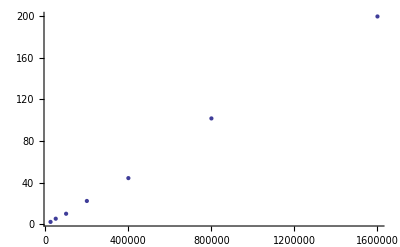

```mathematica
ListPlot[timing]
```

```mathematica
thing=LinearModelFit[timing,x,x]
```

FittedModel[-2.28881+0.000126293 x]

```mathematica
thing["RSquared"]
```

0.99912

Seconds to hours function to make timing human-readable.

```mathematica
stoh[t_]:=t/(60*60);
```